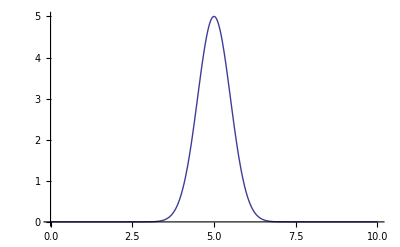

```mathematica
Plot[5 E^((-(2x-10)^2)/2),{x,0,10},PlotRange->All]
```

```mathematica
Plot3D[(2π)/(2π (Subscript[σ, x] Subscript[σ, y])) E^((-(x-Subscript[x, 0])^2)/(2 Subscript[σ, x])-(y-Subscript[y, 0])^2/(2 Subscript[σ, y]))/.{Subscript[σ, x]->2,Subscript[σ, y]->2,Subscript[x, 0]->1,Subscript[y, 0]->1},{x,-5,5},{y,-5,5},PlotRange->{0,0.5}]
```

-Graphics3D-

```mathematica
Integrate[(1/(2π (Subscript[σ, x] Subscript[σ, y])Erf[1/(√2)]^2) E^((-(x-Subscript[x, 0])^2)/(2 Subscript[σ, x]^2)-(y-Subscript[y, 0])^2/(2 Subscript[σ, y]^2)))/.{Subscript[σ, x]->4,Subscript[σ, y]->4,Subscript[x, 0]->0,Subscript[y, 0]->0},{x,-4,4},{y,-4,4}]
```

1

```mathematica
Integrate[E^(-x^2/2),{x,-1,1}]/Integrate[E^(-x^2/2),{x,-∞,∞}]
```

Erf[1/(√2)]

```mathematica
Integrate[E^(-x^2/2-y^2/2),{x,-1,1},{y,-1,1}]/Integrate[E^(-x^2/2-y^2/2),{x,-∞,∞},{y,-∞,∞}]
```

Erf[1/(√2)]^2